```mathematica
Reduce[-x+a y+x^2 y==0&&b-a y - x^2 y ==0&&a>0&&b>0&&x≥0&&y≥0]
toGetY=(x-x^2 y)/y/.{x->b};
Solve[toGetY==a,y]
equilibriumPoint={b,b/(a+b^2)}
j[{x0_,y0_}]:=Grad[{-x+a y+x^2 y,b-a y - x^2 y },{x,y}]/.{x->x0,y->y0}
jacobian=j@equilibriumPoint
det=Det@jacobian
tr=Tr@jacobian
(* Periodic orbit if the equilibrium point is stable node *)
Reduce[tr>0&& a>0 && b>0,a,Reals]
```

y>0&&0<x<1/y&&b==x&&a==(x-x^2 y)/y

{{y→b/(a+b^2)}}

{b,b/(a+b^2)}

{{-1+(2 b^2)/(a+b^2),a+b^2},{-(2 b^2)/(a+b^2),-a-b^2}}

a+3 b^2-(2 a b^2)/(a+b^2)-(2 b^4)/(a+b^2)

-1-a-b^2+(2 b^2)/(a+b^2)

0<b<1&&0<a<1/2 (-1-2 b^2)+1/2 √(1+8 b^2)

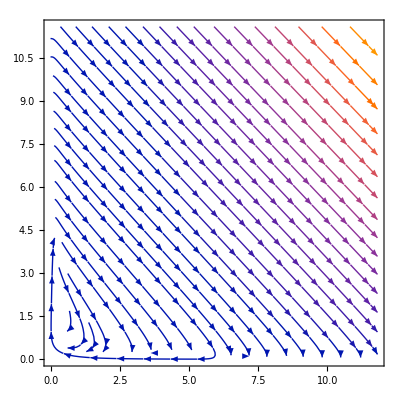

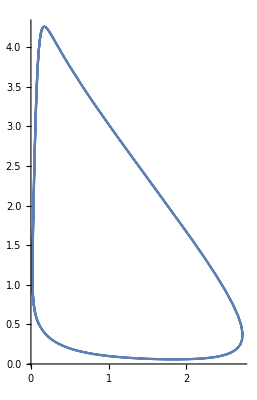

```mathematica
bb=0.2;
aa=1/4 (-1-2 bb^2)+1/4 √(1+8 bb^2);
StreamPlot[{-x+aa y+x^2 y,bb-aa y - x^2 y},{x,0,bb+bb/aa},{y,0,bb/aa}]
sol=NDSolveValue[{x'[t]==-x[t]+aa y[t]+x[t]^2 y[t],y'[t]==bb-aa y[t] - x[t]^2 y[t],x[0]== 0.1,y[0]==0.5} ,{x,y},{t,0,100}];
ParametricPlot[Through[sol[t]],{t,0,100},PlotRange->All]
```

```mathematica
(* Задача 3 *)
σ=10;
λ=24;
b=2;
lorentz=NDSolveValue[{x1'[t]==σ(x2[t]-x1[t]),x2'[t]==(1+λ-x3[t])x1[t]-x2[t],x3'[t]==x1[t]x2[t]-b x3[t],x1[0]==2,x2[0]==3,x3[0]==4},{x1,x2,x3},{t,0,100}];
lorentz2=NDSolveValue[{x1'[t]==σ(x2[t]-x1[t]),x2'[t]==(1+λ-x3[t])x1[t]-x2[t],x3'[t]==x1[t]x2[t]-b x3[t],x1[0]==2.004,x2[0]==3.1,x3[0]==4.01},{x1,x2,x3},{t,0,100}];
ParametricPlot3D[Through[lorentz[t]],{t,0,100},PlotRange->All, PlotStyle->Orange]
Manipulate[GraphicsGrid[{ParametricPlot3D[Through[#[t]],{t,0,tt},PlotRange->All, PlotStyle->Orange]}&/@{lorentz,lorentz2}],{tt,0.01,100}];
```

-Graphics3D-